# Risanje grafov

Povzeto po: Bor Plestenjak: Tečaj iz Mathematice 3. del
Priredila: Alen Orbanić, Matjaž Željko

## Dvorazsežna grafika

### Risanje eksplicitno podanih krivulj

V Mathematici rišemo grafe funkcij s pomočjo ukaza Plot.

#### Plot[f, {x, min, max}]

Plot[f, {x, min, max}] konstruira graf funkcije f, odvisne od spremenljivke x, za vrednosti x od min do max, in ga nariše s privzetimi nastavitvami.

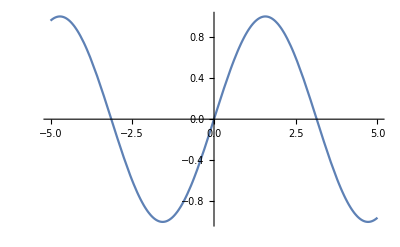

```mathematica
slika1=Plot[Sin[x],{x,-5,5}]
```

#### Export[datoteka, objekt]

Graf (ali druge grafične objekte) lahko shranimo na datoteko z ukazom Export[]. Format datoteke se avtomatično določi glede na podaljšek imena datoteke, lahko pa ga tudi posebej določimo z ukazom Export[datoteka, objekt, format]. Pred shranjevanjem je koristno nastaviti mapo, v katero naj se datoteka zapiše. Velikost slike določimo z izbirnim parametrom ImageSize -> {širina, višina}, kjer podamo mere v tiskarskih točkah (1pt = 1/72 inče). Priporočljivo je nastaviti le eno dimenzijo, drugo pa pustimo na Automatic. Podobno lahko s parametrom ImageResolution podamo ločljivost bitne slike (v enotah dpi).

```mathematica
SetDirectory[NotebookDirectory[]];
Export["GrafSinus.eps", slika1]
Export["GrafSinus.pdf", slika1, ImageSize->{Automatic,100}]
Export["GrafSinus.png", slika1, ImageResolution->600]
```

GrafSinus.eps

GrafSinus.pdf

GrafSinus.png

#### Risanje več funkcij hkrati

Namesto ene funkcije lahko ukazu Plot kot prvi argument podamo tudi seznam funkcij.

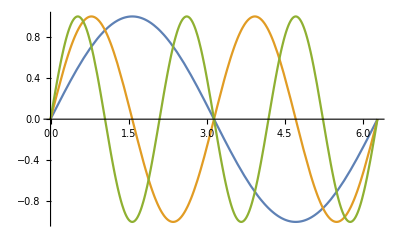

```mathematica
slika2=Plot[{Sin[x],Sin[2 x],Sin[3 x]},{x,0,2 π}]
```

Tako lahko npr. narišemo nekaj premic z različnimi nakloni.

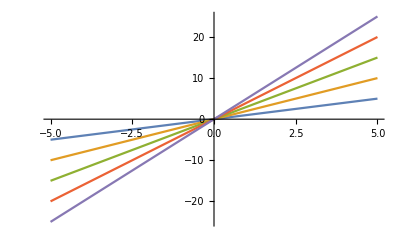

```mathematica
premice=Table[k x,{k,5}];
slika3=Plot[premice,{x,-5,5}]
```

#### Določanje območja izrisa

Medtem ko interval risanja po osi x določamo z drugim argumentom funkcije Plot, lahko z izbirnim parametrom PlotRange->{{xmin, xmax},{ymin, ymax}} oziroma  PlotRange->{ymin, ymax} nastavimo območje izrisa na obeh oseh oziroma le na osi y.

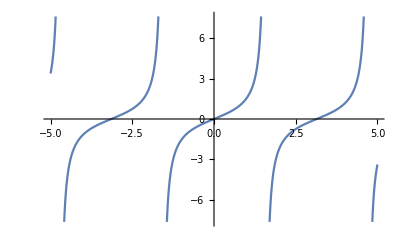

```mathematica
slika4=Plot[Tan[x],{x,-5,5}]
```

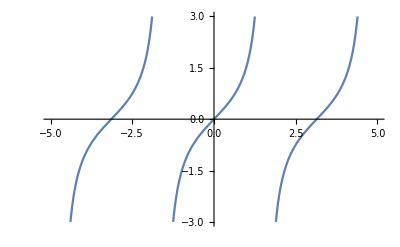

```mathematica
slika4=Plot[Tan[x],{x,-5,5},PlotRange->{-3,3}]
```

#### Spreminjanje razmerja enot na oseh

Opcija AspectRatio določa razmerje med višino in širino slike. Ukaz Plot določi sam razmerje enot v smeri x in y. Če nastavimo AspectRatio -> Automatic, bo razmerje 1:1.

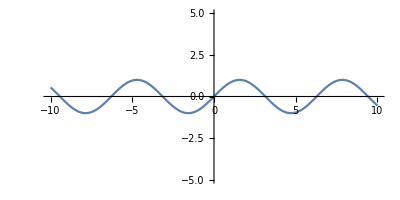

```mathematica
slika5 =Plot[Sin[x], {x,-10, 10}, AspectRatio->Automatic,PlotRange->{-5,5}]
```

#### Hkratno prikazovanje več slik

S pomočjo ukaza Show lahko hkrati prikažemo več slik v istem koordinatnem sistemu.

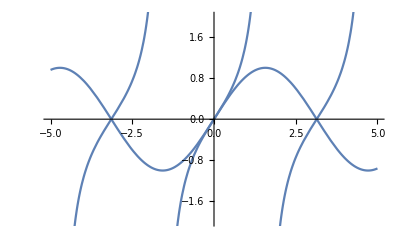

```mathematica
Show[slika1,slika4,PlotRange->{-2,2}]
```

Grafični objekt se nariše le na tistem delu območja, nad katerim smo ga konstruirali.

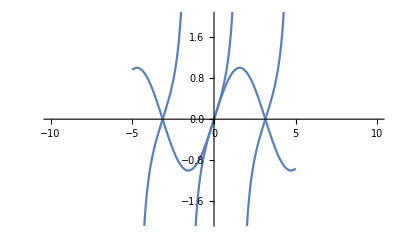

```mathematica
Show[slika1,slika4,PlotRange->{{-10,10}, {-2,2}}]
```

#### Tabele slik

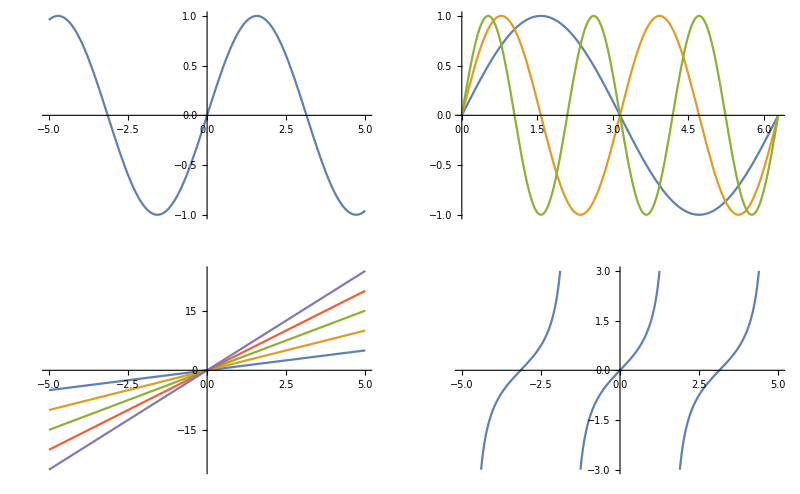

```mathematica
slike=GraphicsGrid[{{slika1,slika2},{slika3,slika4}}]
```

#### Osi, okvir in merske enote na oseh

Z izbirnim parametrom Frame -> True dodamo sliki okvir z označenimi enotami. Izbirni parameter Axes -> False izklopi izris koordinatnih osi. Oba parametra delujeta tako pri ukazu Plot kot pri ukazu Show.

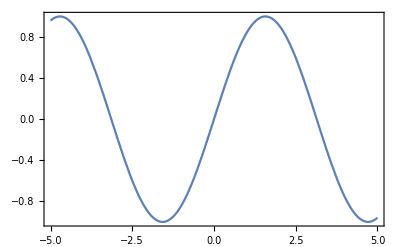

```mathematica
Show[slika1, Frame -> True, Axes -> False]
```

Če želimo sami določiti oznake na koordinatnih oseh, uporabimo izbirni parameter Ticks -> {seznamX, seznamY}, kjer seznamX vsebuje točk, ki naj bodo označene na osi x, seznamY pa točke, ki naj bodo označene na osi y. V koordinatnem izhodišču se oznaka ne izpiše - dodamo jo lahko z ukazom Text (glej spodaj).

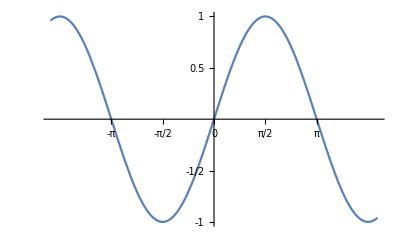

```mathematica
Show[slika1,Ticks -> {{-Pi, -Pi/2, 0, Pi/2, Pi}, {-1, -1/2, 0.5, 1}}]
```

Če v katerega od seznamov izbirnega parametra Ticks vključimo par {tč, oz}, se v točki tč izpiše oznaka oz (ki je običajno niz, t.j. besedilo v navednicah).

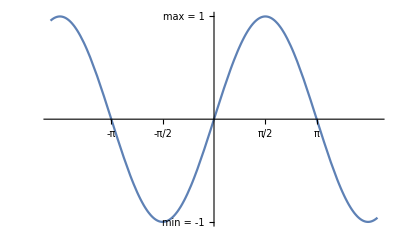

```mathematica
Show[slika1, Ticks->{{-Pi,-Pi/2,Pi/2,Pi},
{{-1,"min = -1"},{1,"max = 1"}}}]
```

#### Opremljanje slike z naslovom in opisi osi

Za določanje naslova grafa uporabimo izbirni parameter PlotLabel -> naslov, kjer je naslov ponavadi besedilo v navednicah.
Za določanje opisov osi uporabimo izbirni parameter AxesLabel -> {opisOsiX, opisOsiY}, kjer sta opisa besedili v navednicah.

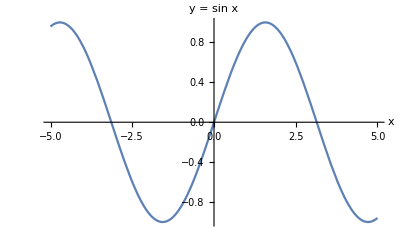

```mathematica
Show[slika1,AxesLabel->{"x","y = sin x"}]
```

Z izbirnim parametrom FrameLabel ->{napisSpodaj, napisLevo, napisZgoraj, napisDesno} določimo napise ob okvirju. Napisi so besedila v navednicah.

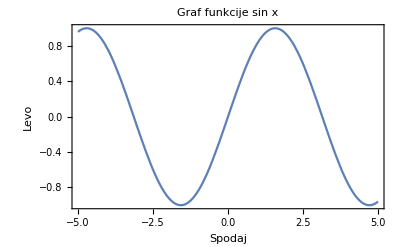

```mathematica
Show[slika1,PlotLabel->"Graf funkcije sin x",Frame->True,
FrameLabel->{"Spodaj","Levo","Zgoraj","Desno"}]
```

#### Opremljanje slik z dodatnim besedilom

Z ukazom Text[besedilo, {x, y}, poravnava] izpišemo dano besedilo v točki (x, y). Elementi seznama poravnava so lahko Top, Bottom, Center, Left, Right. Če seznam poravnava izpustimo, je privzeta vrednost Center.

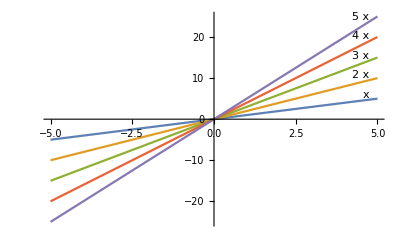

```mathematica
oznake = Graphics[Table[ Text[k x, {4.75,4.75k}, {Right,Bottom}],{k,5}]];
Show[slika3, oznake]
```

#### Različne oblike črt

Z izbirnim parametrom PlotStyle določimo lastnosti krivulje grafa, kot so npr.:

RGBColor[r,g,b] ... aditivna mešanica rdeče, zelene in modre barve. Intenzivnosti r, g, b so med 0 in 1, npr.:

    RGBColor[1,0,0] ... rdeča
    RGBColor[0,1,0] ... zelena
    RGBColor[1,1,0] ... rumena
    
Obstaja nekaj vgrajenih barv: Blue, Yellow, Green, Orange, Red  ipd.

Thickness[d] ... debelina izrisane črte

Dashing[vzorec] ... vzorec črtkanja črte, podan v seznamu vzorec. Vzorec {0.01, 0.01} npr. pomeni črtkano črto, kjer vsaka črtica in vsak presledek predstavlja 1% celotne širine slike.

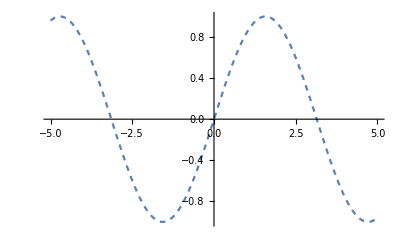

```mathematica
Plot[Sin[x],{x,-5,5},PlotStyle->Dashing[{0.01,0.01}]]
```

Če rišemo več funkcij hkrati, Plot avtomatično izmenjuje barve krivulj. Lahko pa za vsako krivuljo podamo lastnosti, tako da pri izbirnem parametru PlotStyle navedemo seznam.

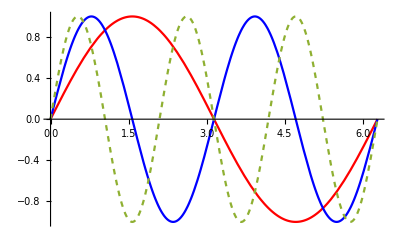

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[3 x]},{x,0,2 π},
PlotStyle->{Red,Blue,Dashing[{0.01,0.01}]}]
```

Če želimo za določeno krivuljo podati več lastnosti, uporabimo podseznam.

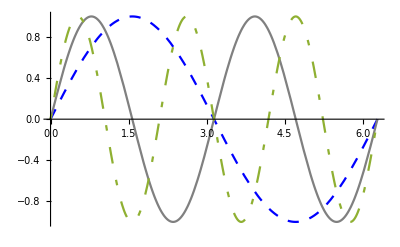

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[3 x]},{x,0,2 π},PlotStyle->{{Blue,Dashing[{0.02,0.02}]},GrayLevel[0.5],Dashing[{0.01,0.03,0.03,0.03}]}]
```

### Risanje zaporedij in točk

#### ListPlot[sez], ListLinePlot[sez]

ListPlot nariše zaporedje točk, katerih ordinate so elementi seznama sez, abscise pa zaporedna naravna števila 1, 2, 3, ... .

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}

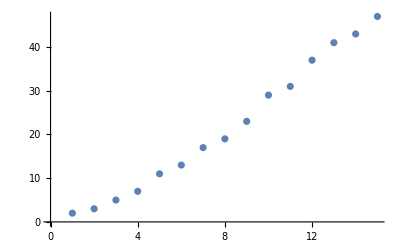

```mathematica
praštevila=Table[Prime[i],{i,1,15}]
ListPlot[praštevila]
```

Ukazu ListPlot lahko kot argument podamo tudi seznam koordinat točk. Z izbirnim parametrom Joined->True povežemo zaporedne točke, kar je enakovredno ukazu ListLinePlot.

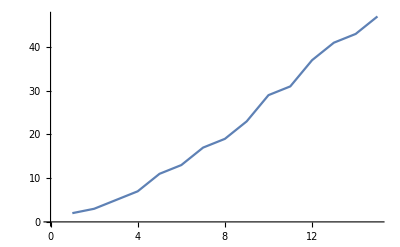

```mathematica
ListLinePlot[praštevila]
```

### Risanje implicitno podanih krivulj

#### ContourPlot[enačba, {x, xmin, xmax}, {y, ymin, ymax}]

ContourPlot nariše krivuljo, ki jo določa enačba z neznankama x in y na območju [xmin,xmax] × [ymin, ymax].

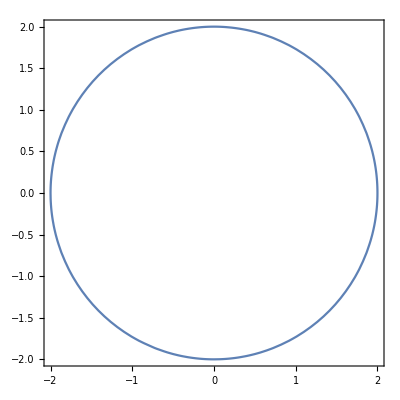

```mathematica
ContourPlot[x^2+y^2==4,{x,-2,2},{y,-2,2}]
```

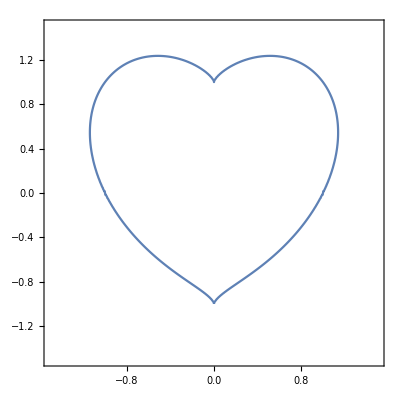

```mathematica
ContourPlot[(x^2+y^2-1)^3-x^2 y^3==0,{x,-1.5,1.5},{y,-1.5,1.5},PlotPoints->100]
```

Če kot prvi argument ukazu ContourPlot podamo seznam enačb, lahko na isti sliki dobimo več implicitno določenih krivulj:

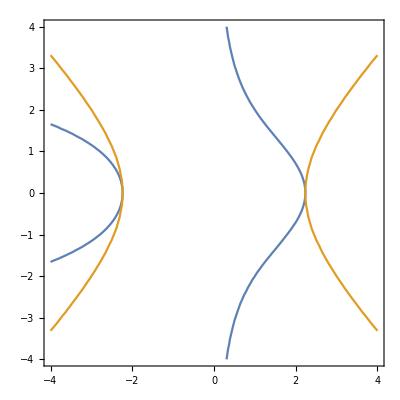

```mathematica
ContourPlot[{x^2+x y^2==5,x^2-y^2==5},{x,-4,4},{y,-4,4}]
```

### Risanje parametrično podanih krivulj

#### ParametricPlot[{fx, fy}, {t, tmin, tmax}]

Nariše parametrično podano krivuljo, kjer sta fx in fy funkciji odvisni od parametra t, pri čemer t teče od tmin do tmax.

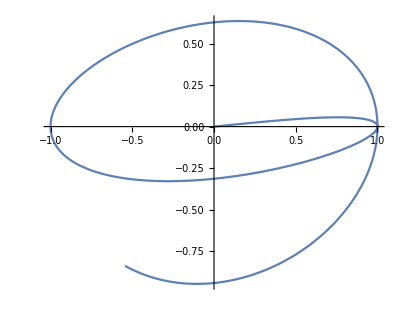

```mathematica
ParametricPlot[{Sin[t],1/10 t Cos[t]},{t,0,10}]
```

### Risanje območij v ravnini

#### RegionPlot[p, {x, xmin, xmax}, {y, ymin, ymax}]

Nariše množico točk v pravokotniku [xmin,xmax] × [ymin, ymax], ki zadoščajo pogoju p.

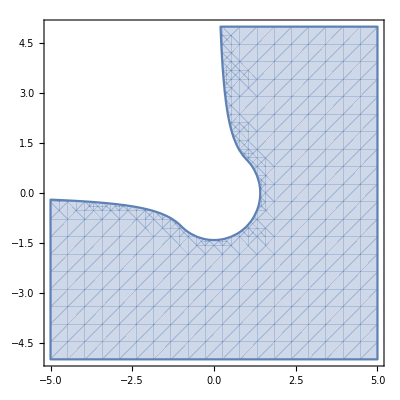

```mathematica
RegionPlot[x+Sqrt[y^2+x^2-2]>y,{x,-5,5},{y,-5,5}]
```

### Notranja struktura dvorazsežne grafike

Dvorazsežne slike v Mathematici (vključno s tistimi, ki jih konstruirajo ukazi Plot, ParametricPlot, ListPlot ipd.) so izrazi z glavo Graphics, argumenti pa so osnovni grafični objekti (npr.  Point, Line, Circle, Disk, Polygon), grafična določila (npr. RGBColor, Thichness, Dashing ipd.), različne ovojnice in izbirni parametri.

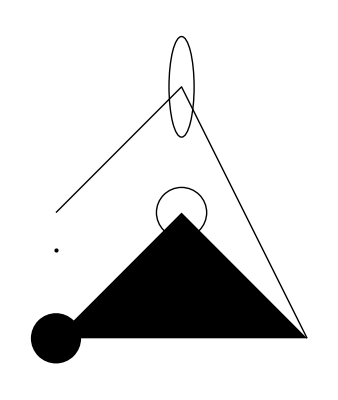

```mathematica
Show[Graphics[{Point[{1,1.7}], Line[{{1,2},{2,3},{3,1}}], Circle[{2,2},0.2],
Circle[{2,3},{0.1,0.4}], Disk[{1,1},0.2], Polygon[{{1,1},{2,2},{3,1},{1,1}}]}]]
```

Zgled grafičnega objekta, ki ga konstruira ukaz Plot:

```mathematica
slika1//InputForm
```

Graphics[
 {{{{}, {}, Annotation[
     {Directive[Opacity[1.], 
       RGBColor[0.368417, 0.506779, 
        0.709798], AbsoluteThickness[
        1.6]], Line[
       {{-4.9999997959183675, 
       0.9589243325533604}, 
       {-4.996932820794404, 
       0.959789805476791}, 
       {-4.99386584567044, 
       0.9606462503015046}, 
       {-4.987731895422513, 
       0.9623320235157689}, 
       {-4.975463994926658, 
       0.9655948839945871}, 
       {-4.950928193934949, 
       0.9716841711368529}, 
       {-4.947861218810986, 
       0.9724042754918903}, 
       {-4.9447942436870225, 
       0.9731152330923547}, 
       {-4.938660293439095, 
       0.9745096813656606}, 
       {-4.9263923929432405, 
       0.9771885283795209}, 
       {-4.901856591951532, 
       0.9821046422353232}, 
       {-4.898789616827568, 
       0.9826776443426876}, 
       {-4.895722641703605, 
       0.9832414030607912}, 
       {-4.889588691455677, 
       0.9843411692046127}, 
       {-4.877320790959823, 
       0.9864295533249994}, 
       {-4.87425381583586, 
       0.9869284647122559}, 
       {-4.871186840711896, 
       0.9874180927256367}, 
       {-4.865052890463969, 
       0.9883694802957279}, 
       {-4.852784989968114, 
       0.9901606581587687}, 
       {-4.849718014844151, 
       0.9905851784935705}, 
       {-4.846651039720188, 
       0.9910003810582434}, 
       {-4.84051708947226, 
       0.991802817342758}, 
       {-4.828249188976406, 
       0.9932957107035676}, 
       {-4.825182213852441, 
       0.9936455844351461}, 
       {-4.822115238728478, 
       0.9939861116094103}, 
       {-4.81598128848055, 
       0.9946391135615008}, 
       {-4.803713387984696, 
       0.9958328237351057}, 
       {-4.800388435502832, 
       0.9961305459733428}, 
       {-4.797063483020969, 
       0.9964172556907287}, 
       {-4.79041357805724, 
       0.9969576250060824}, 
       {-4.787088625575377, 
       0.9972112786301061}, 
       {-4.783763673093513, 
       0.9974539077854561}, 
       {-4.7771137681297855, 
       0.9979060820826925}, 
       {-4.773788815647922, 
       0.9981156222256569}, 
       {-4.770463863166058, 
       0.9983141279021591}, 
       {-4.767138910684194, 
       0.9985015969176594}, 
       {-4.763813958202331, 
       0.9986780271996318}, 
       {-4.760489005720467, 
       0.9988434167975869}, 
       {-4.757164053238603, 
       0.9989977638830934}, 
       {-4.750514148274876, 
       0.9992733238134445}, 
       {-4.747189195793013, 
       0.9993945336118917}, 
       {-4.743864243311148, 
       0.9995046948051293}, 
       {-4.740539290829284, 
       0.999603806175292}, 
       {-4.737214338347421, 
       0.9996918666266742}, 
       {-4.733889385865557, 
       0.9997688751857412}, 
       {-4.730564433383693, 
       0.9998348310011405}, 
       {-4.727239480901829, 
       0.9998897333437107}, 
       {-4.723914528419965, 
       0.9999335816064902}, 
       {-4.720589575938101, 
       0.9999663753047231}, 
       {-4.717264623456238, 
       0.9999881140758654}, 
       {-4.713939670974374, 
       0.9999987976795884}, 
       {-4.71061471849251, 
       0.9999984259977819}, 
       {-4.707289766010646, 
       0.9999869990345547}, 
       {-4.703964813528782, 
       0.9999645169162354}, 
       {-4.700639861046918, 
       0.9999309798913706}, 
       {-4.697314908565055, 
       0.999886388330722}, 
       {-4.6939899560831915, 
       0.9998307427272627}, 
       {-4.690665003601327, 
       0.9997640436961714}, 
       {-4.687340051119463, 
       0.999686291974826}, 
       {-4.6840150986376, 
       0.9995974884227948}, 
       {-4.680690146155736, 
       0.9994976340218277}, 
       {-4.677365193673872, 
       0.999386729875845}, 
       {-4.674040241192008, 
       0.999264777210925}, 
       {-4.670715288710144, 
       0.999131777375291}, 
       {-4.66739033622828, 
       0.9989877318392959}, 
       {-4.664065383746417, 
       0.9988326421954062}, 
       {-4.6574154787826885, 
       0.9984893375642692}, 
       {-4.654090526300825, 
       0.9983011263723571}, 
       {-4.650765573818961, 
       0.998101878663179}, 
       {-4.644115668855234, 
       0.9976702826259841}, 
       {-4.64079071637337, 
       0.9974379390693905}, 
       {-4.637465763891506, 
       0.9971945685383244}, 
       {-4.630815858927779, 
       0.9966747574367874}, 
       {-4.6274909064459155, 
       0.9963983226129834}, 
       {-4.624165953964051, 
       0.9961108723079776}, 
       {-4.617516049000324, 
       0.9955029380875007}, 
       {-4.614191096518461, 
       0.9951824608929241}, 
       {-4.610866144036597, 
       0.9948509816588601}, 
       {-4.604216239072869, 
       0.9941550318522687}, 
       {-4.590916429145413, 
       0.9926312771518961}, 
       {-4.587811815632181, 
       0.9922502954021712}, 
       {-4.584707202118947, 
       0.9918597497315585}, 
       {-4.57849797509248, 
       0.9910499817770979}, 
       {-4.566079521039546, 
       0.9893158506193389}, 
       {-4.562974907526312, 
       0.9888584680610432}, 
       {-4.559870294013079, 
       0.9883915542743856}, 
       {-4.553661066986613, 
       0.987429151109423}, 
       {-4.541242612933679, 
       0.9853901742066378}, 
       {-4.538137999420446, 
       0.9848566729717633}, 
       {-4.535033385907212, 
       0.9843136790802984}, 
       {-4.528824158880746, 
       0.9831992343538846}, 
       {-4.516405704827813, 
       0.9808566694291854}, 
       {-4.491568796721946, 
       0.9757181327354014}, 
       {-4.488464183208713, 
       0.9750334281526188}, 
       {-4.485359569695479, 
       0.9743393255957434}, 
       {-4.479150342669013, 
       0.9729229534109897}, 
       {-4.46673188861608, 
       0.9699777337817707}, 
       {-4.441894980510213, 
       0.9636390134776713}, 
       {-4.4387903669969795, 
       0.9628047946999606}, 
       {-4.435685753483746, 
       0.9619612958152753}, 
       {-4.42947652645728, 
       0.9602464903350029}, 
       {-4.4170580724043464, 
       0.9567058818011994}, 
       {-4.392221164298479, 
       0.9491826153873361}, 
       {-4.389177450978366, 
       0.9482202848939545}, 
       {-4.386133737658252, 
       0.9472491699137384}, 
       {-4.380046311018026, 
       0.9452806225604519}, 
       {-4.367871457737573, 
       0.9412385153039365}, 
       {-4.343521751176668, 
       0.9327363747506685}, 
       {-4.294822338054859, 
       0.9140784630558778}, 
       {-4.291778624734746, 
       0.912839891353071}, 
       {-4.2887349114146325, 
       0.9115928629338922}, 
       {-4.282647484774406, 
       0.9090734822354579}, 
       {-4.270472631493954, 
       0.9039337537968}, 
       {-4.246122924933049, 
       0.8932531212743864}, 
       {-4.197423511811239, 
       0.8703097297101476}, 
       {-4.194121821133226, 
       0.8686788904806642}, 
       {-4.190820130455213, 
       0.8670385816510512}, 
       {-4.184216749099186, 
       0.863729626819491}, 
       {-4.1710099863871335, 
       0.8569988756223439}, 
       {-4.144596460963027, 
       0.8430901501833516}, 
       {-4.091769410114814, 
       0.8135183083636784}, 
       {-3.986115308418389, 
       0.7476541980484731}, 
       {-3.983033956709006, 
       0.7456043624468265}, 
       {-3.979952604999623, 
       0.7435474475398977}, 
       {-3.973789901580857, 
       0.7394124579965572}, 
       {-3.9614644947433257, 
       0.7310583910397518}, 
       {-3.936813681068263, 
       0.7140183696725839}, 
       {-3.8875120537181376, 
       0.6786473637286828}, 
       {-3.788908799017886, 
       0.6030476555583278}, 
       {-3.575191738711772, 
       0.42013954052545777}, 
       {-3.3653722907653534, 
       0.22191659380276585}, 
       {-3.169654536811282, 
       0.02805820038795528}, 
       {-2.9574262319516, 
       -0.18312711532548273}, 
       {-2.759299621084266, 
       -0.3730489505938499}, 
       {-2.565070622576627, 
       -0.5451114369829408}, 
       {-2.5617778171170453, 
       -0.5478690450234396}, 
       {-2.558485011657463, 
       -0.5506207127620428}, 
       {-2.551899400738299, 
       -0.5561061080578247}, 
       {-2.5387281788999707, 
       -0.5670043066365581}, 
       {-2.5123857352233143, 
       -0.5885037409535488}, 
       {-2.459700847870002, 
       -0.6302629144554899}, 
       {-2.354331073163377, 
       -0.7084231875901441}, 
       {-2.3512586066724253, 
       -0.7105883501380159}, 
       {-2.3481861401814736, 
       -0.7127468047013698}, 
       {-2.3420412071995704, 
       -0.7170435084344249}, 
       {-2.329751341235764, 
       -0.7255555278128508}, 
       {-2.305171609308151, 
       -0.7422495361397345}, 
       {-2.256012145452926, 
       -0.7742824864173556}, 
       {-2.2529396789619742, 
       -0.7762232088244319}, 
       {-2.249867212471023, 
       -0.7781566036511073}, 
       {-2.24372227948912, 
       -0.7820013376272819}, 
       {-2.2314324135253134, 
       -0.7896020762120062}, 
       {-2.2068526815977005, 
       -0.8044446414899322}, 
       {-2.157693217742475, 
       -0.8326631245766082}, 
       {-2.154362773893623, 
       -0.8345028359726877}, 
       {-2.1510323300447713, 
       -0.8363332911918422}, 
       {-2.144371442347068, 
       -0.8399663519897611}, 
       {-2.1310496669516605, 
       -0.8471205130312639}, 
       {-2.1044061161608463, 
       -0.8609765841668695}, 
       {-2.051119014579218, 
       -0.8868458661026289}, 
       {-2.0477885707303667, 
       -0.8883798276612519}, 
       {-2.0444581268815147, 
       -0.8899039354476566}, 
       {-2.037797239183811, 
       -0.8929225221926199}, 
       {-2.024475463788404, 
       -0.8988407139343271}, 
       {-1.9978319129975897, 
       -0.9101975315447733}, 
       {-1.9445448114159614, 
       -0.9309652887730411}, 
       {-1.9412752677602296, 
       -0.9321540462378962}, 
       {-1.9380057241044981, 
       -0.9333328390634388}, 
       {-1.931466636793035, 
       -0.9356604804985033}, 
       {-1.918388462170109, 
       -0.9401956403981377}, 
       {-1.8922321129242567, 
       -0.9487827895175204}, 
       {-1.888962569268525, 
       -0.9498106605765276}, 
       {-1.8856930256127935, 
       -0.9508283782486713}, 
       {-1.8791539383013305, 
       -0.9528333100237973}, 
       {-1.8660757636784044, 
       -0.9567208615285072}, 
       {-1.8399194144325521, 
       -0.9640044258721925}, 
       {-1.8366498707768204, 
       -0.9648685982759003}, 
       {-1.833380327121089, 
       -0.965722456324803}, 
       {-1.8268412398096259, 
       -0.9673991929579009}, 
       {-1.8137630651866998, 
       -0.970628499748577}, 
       {-1.8104935215309683, 
       -0.971409907925973}, 
       {-1.8072239778752368, 
       -0.9721809318225776}, 
       {-1.8006848905637738, 
       -0.9736917939158147}, 
       {-1.7876067159408475, 
       -0.9765885515253786}, 
       {-1.7843371722851158, 
       -0.9772866609029381}, 
       {-1.7810676286293843, 
       -0.977974323177768}, 
       {-1.7745285413179213, 
       -0.9793182771268153}, 
       {-1.7614503666949952, 
       -0.9818805038381935}, 
       {-1.735294017449143, 
       -0.9865007363798839}, 
       {-1.7322448127620418, 
       -0.9869954776134074}, 
       {-1.7291956080749409, 
       -0.9874810421163047}, 
       {-1.7230971987007386, 
       -0.9884246229571652}, 
       {-1.7109003799523341, 
       -0.9902014709504222}, 
       {-1.707851175265233, 
       -0.9906226767132167}, 
       {-1.7048019705781319, 
       -0.9910346720209862}, 
       {-1.6987035612039296, 
       -0.991831016034782}, 
       {-1.6865067424555251, 
       -0.9933130157982323}, 
       {-1.683457537768424, 
       -0.9936604354644262}, 
       {-1.6804083330813229, 
       -0.9939986164316017}, 
       {-1.6743099237071206, 
       -0.9946472497776828}, 
       {-1.6712607190200195, 
       -0.9949576961258276}, 
       {-1.6682115143329184, 
       -0.9952588917134889}, 
       {-1.6621131049587163, 
       -0.9958335194917619}, 
       {-1.6590639002716152, 
       -0.9961069463396902}, 
       {-1.6560146955845143, 
       -0.9963711117418179}, 
       {-1.649916286210312, 
       -0.9968716484703423}, 
       {-1.646867081523211, 
       -0.9971080151429276}, 
       {-1.6438178768361098, 
       -0.9973351110621329}, 
       {-1.6377194674619076, 
       -0.9977614822807929}, 
       {-1.6346702627748064, 
       -0.9979607536160006}, 
       {-1.6316210580877053, 
       -0.9981507462693712}, 
       {-1.625522648713503, 
       -0.9985028885509526}, 
       {-1.622473444026402, 
       -0.9986650349050705}, 
       {-1.6194242393393008, 
       -0.998817896029196}, 
       {-1.6133258299650988, 
       -0.9990957569888217}, 
       {-1.6102766252779976, 
       -0.9992207542408702}, 
       {-1.6072274205908967, 
       -0.9993364610960467}, 
       {-1.6041782159037956, 
       -0.9994428764785505}, 
       {-1.6011290112166945, 
       -0.9995399993989693}, 
       {-1.5980798065295934, 
       -0.9996278289542891}, 
       {-1.5950306018424922, 
       -0.999706364327902}, 
       {-1.591981397155391, 
       -0.9997756047896144}, 
       {-1.58893219246829, 
       -0.9998355496956531}, 
       {-1.5858829877811889, 
       -0.9998861984886719}, 
       {-1.5828337830940877, 
       -0.9999275506977563}, 
       {-1.5797845784069866, 
       -0.9999596059384285}, 
       {-1.5767353737198855, 
       -0.9999823639126503}, 
       {-1.5736861690327844, 
       -0.999995824408826}, 
       {-1.5706369643456832, 
       -0.999999987301805}, 
       {-1.5675877596585823, 
       -0.9999948525528819}, 
       {-1.5645385549714812, 
       -0.999980420209798}, 
       {-1.56148935028438, 
       -0.9999566904067401}, 
       {-1.5584401455972792, 
       -0.9999236633643392}, 
       {-1.555390940910178, 
       -0.9998813393896692}, 
       {-1.552341736223077, 
       -0.9998297188762428}, 
       {-1.5492925315359758, 
       -0.9997688023040096}, 
       {-1.5462433268488747, 
       -0.9996985902393497}, 
       {-1.5431941221617735, 
       -0.99961908333507}, 
       {-1.5401449174746724, 
       -0.999530282330397}, 
       {-1.5368377354296712, 
       -0.9994234624440226}, 
       {-1.53353055338467, 
       -0.9993057114203852}, 
       {-1.5302233713396687, 
       -0.9991770305473797}, 
       {-1.5269161892946674, 
       -0.9990374212324461}, 
       {-1.5236090072496662, 
       -0.9988868850025531}, 
       {-1.520301825204665, 
       -0.9987254235041824}, 
       {-1.5136874611146622, 
       -0.9983697318853864}, 
       {-1.5103802790696608, 
       -0.9981755056553179}, 
       {-1.5070730970246595, 
       -0.9979703619374428}, 
       {-1.500458732934657, 
       -0.9975273311326484}, 
       {-1.4971515508896558, 
       -0.9972894488913532}, 
       {-1.4938443688446545, 
       -0.9970406588534468}, 
       {-1.487230004754652, 
       -0.9965103663915815}, 
       {-1.4839228227096508, 
       -0.9962288697676662}, 
       {-1.4806156406646496, 
       -0.9959364769471636}, 
       {-1.474001276574647, 
       -0.9953190156276568}, 
       {-1.4607725483946419, 
       -0.993953487323323}, 
       {-1.4574653663496404, 
       -0.9935849173408582}, 
       {-1.4541581843046392, 
       -0.9932054800798852}, 
       {-1.4475438202146367, 
       -0.9924140204415234}, 
       {-1.4343150920346317, 
       -0.9907008843838777}, 
       {-1.4310079099896305, 
       -0.9902454990256948}, 
       {-1.4277007279446292, 
       -0.9897792829137015}, 
       {-1.4210863638546267, 
       -0.988814378943538}, 
       {-1.4078576356746215, 
       -0.9867548342527255}, 
       {-1.40455045362962, 
       -0.9862129522686134}, 
       {-1.4012432715846188, 
       -0.9856602836364418}, 
       {-1.3946289074946163, 
       -0.9845226107249588}, 
       {-1.3814001793146113, 
       -0.982118098991983}, 
       {-1.37809299726961, 
       -0.9814900996755773}, 
       {-1.3747858152246089, 
       -0.9808513653670435}, 
       {-1.3681714511346061, 
       -0.9795417198354095}, 
       {-1.354942722954601, 
       -0.9767939241130815}, 
       {-1.3284852665945908, 
       -0.9707860363050513}, 
       {-1.32539842351822, 
       -0.9700407342192965}, 
       {-1.3223115804418493, 
       -0.9692861890105683}, 
       {-1.3161378942891075, 
       -0.9677493980712127}, 
       {-1.303790521983624, 
       -0.9645652209584505}, 
       {-1.2790957773726572, 
       -0.9577562142986537}, 
       {-1.2760089342962864, 
       -0.9568639341689764}, 
       {-1.2729220912199155, 
       -0.9559625364726854}, 
       {-1.2667484050671738, 
       -0.9541324228232634}, 
       {-1.2544010327616906, 
       -0.9503631684539791}, 
       {-1.229706288150724, 
       -0.9423905916995017}, 
       {-1.226619445074353, 
       -0.9413535096417285}, 
       {-1.2235326019979822, 
       -0.940307457809858}, 
       {-1.2173589158452405, 
       -0.9381884847788069}, 
       {-1.2050115435397573, 
       -0.9338433457079098}, 
       {-1.1803167989287906, 
       -0.9247266425848599}, 
       {-1.130927309706857, 
       -0.9048074462500607}, 
       {-1.1275824892725859, 
       -0.9033780928678234}, 
       {-1.1242376688383149, 
       -0.9019386326601377}, 
       {-1.117548027969773, 
       -0.8990294562989621}, 
       {-1.104168746232689, 
       -0.8930905378190013}, 
       {-1.0774101827585207, 
       -0.8807341962140571}, 
       {-1.0238930558101846, 
       -0.8541390524432553}, 
       {-1.0205482353759137, 
       -0.8523948216083604}, 
       {-1.0172034149416427, 
       -0.8506410543393376}, 
       {-1.0105137740731007, 
       -0.8471049890886637}, 
       {-0.9971344923360166, 
       -0.8399192918151489}, 
       {-0.9703759288618484, 
       -0.8250981674553385}, 
       {-0.9168588019135122, 
       -0.7936946969018288}, 
       {-0.9135748816723614, 
       -0.7916927586117333}, 
       {-0.9102909614312107, 
       -0.7896822826099791}, 
       {-0.9037231209489092, 
       -0.7856358042882103}, 
       {-0.890587439984306, 
       -0.7774413552183871}, 
       {-0.8643160780550998, 
       -0.7606514664556357}, 
       {-0.8117733541966873, 
       -0.7255087598054979}, 
       {-0.7066879064798623, 
       -0.6493184348654106}, 
       {-0.703624325207342, 
       -0.6469854868567171}, 
       {-0.7005607439348216, 
       -0.6446464665509385}, 
       {-0.694433581389781, 
       -0.6399502969166256}, 
       {-0.6821792562996996, 
       -0.6304860598048905}, 
       {-0.6576706061195369, 
       -0.6112749871594304}, 
       {-0.6086533057592114, 
       -0.5717631256970727}, 
       {-0.5106187050385604, 
       -0.4887171248365867}, 
       {-0.2980389526916474, 
       -0.29364617956975037}, 
       {-0.09956089433708235, 
       -0.09939649507263913}, 
       {0.09501955165778773, 
       0.09487663211369161}, 
       {0.306110548558269, 
       0.3013522831710188}, 
       {0.5030998514664022, 
       0.4821436064217323}, 
       {0.506435786682242, 
       0.48506350506683144}, 
       {0.5097717218980817, 
       0.48797800570529704}, 
       {0.5164435923297612, 
       0.49379068328722137}, 
       {0.5297873331931202, 
       0.505349839349669}, 
       {0.5564748149198383, 
       0.5281961725270359}, 
       {0.6098497783732744, 
       0.5727443247785438}, 
       {0.7165997052801466, 
       0.6568245039459318}, 
       {0.719874740302866, 
       0.6592904958409136}, 
       {0.7231497753255856, 
       0.6617494162883503}, 
       {0.7296998453710246, 
       0.666645937420722}, 
       {0.7427999854619027, 
       0.6763529669754542}, 
       {0.769000265643659, 
       0.6954171709030283}, 
       {0.8214008260071713, 
       0.7321007852556035}, 
       {0.8246758610298908, 
       0.7343277969064076}, 
       {0.8279508960526103, 
       0.7365469322712201}, 
       {0.8345009660980494, 
       0.7409614790191996}, 
       {0.8476011061889275, 
       0.7496950154822657}, 
       {0.8738013863706837, 
       0.7667746434943781}, 
       {0.9262019467341961, 
       0.7993435592734447}, 
       {0.9292566427882851, 
       0.8011753152430229}, 
       {0.9323113388423743, 
       0.8029995953169642}, 
       {0.9384207309505523, 
       0.8066256597572509}, 
       {0.9506395151669087, 
       0.8137873335868758}, 
       {0.9750770835996214, 
       0.8277451425617217}, 
       {1.0239522204650469, 
       0.854169819212867}, 
       {1.0270069165191358, 
       0.8557542556342677}, 
       {1.030061612573225, 
       0.8573307068751663}, 
       {1.0361710046814032, 
       0.8604595950496258}, 
       {1.0483897888977594, 
       0.8666209069963052}, 
       {1.072827357330472, 
       0.878554479078636}, 
       {1.1217024941958975, 
       0.9008408841900525}, 
       {1.1250151676078868, 
       0.9022741339116456}, 
       {1.128327841019876, 
       0.9036974822617697}, 
       {1.1349531878438546, 
       0.9065144124783063}, 
       {1.1482038814918116, 
       0.9120287764952043}, 
       {1.1747052687877257, 
       0.9225761670197951}, 
       {1.178017942199715, 
       0.9238491817015899}, 
       {1.1813306156117043, 
       0.9251120582517623}, 
       {1.1879559624356828, 
       0.9276073416344516}, 
       {1.2012066560836399, 
       0.9324756485168325}, 
       {1.227708043379554, 
       0.9417202687544477}, 
       {1.2310207167915432, 
       0.9428294729609464}, 
       {1.2343333902035325, 
       0.9439283307499955}, 
       {1.240958737027511, 
       0.9460949589548553}, 
       {1.254209430675468, 
       0.9503035353983247}, 
       {1.2807108179713822, 
       0.9582194205711528}, 
       {1.2840234913833715, 
       0.959161698950937}, 
       {1.2873361647953607, 
       0.96009345168677}, 
       {1.2939615116193393, 
       0.9619253394427462}, 
       {1.3072122052672963, 
       0.9654623650858992}, 
       {1.3337135925632102, 
       0.9720272823499281}, 
       {1.3368059270065689, 
       0.9727489239818796}, 
       {1.3398982614499277, 
       0.973461263678229}, 
       {1.3460829303366455, 
       0.9748580101060729}, 
       {1.3584522681100806, 
       0.9775395859844227}, 
       {1.3615446025534395, 
       0.9781866263914101}, 
       {1.3646369369967983, 
       0.9788243128646319}, 
       {1.3708216058835159, 
       0.9800715997077131}, 
       {1.3831909436569512, 
       0.9824536638814748}, 
       {1.38628327810031, 
       0.9830257070936262}, 
       {1.389375612543669, 
       0.9835883500981832}, 
       {1.3955602814303865, 
       0.9846854140533046}, 
       {1.4079296192038218, 
       0.9867665087686261}, 
       {1.4110219536471806, 
       0.9872632047121671}, 
       {1.4141142880905395, 
       0.9877504599269381}, 
       {1.420298956977257, 
       0.9886966296229317}, 
       {1.4326682947506924, 
       0.9904754813104982}, 
       {1.4357606291940512, 
       0.990896526021987}, 
       {1.43885296363741, 
       0.991308095260981}, 
       {1.4450376325241276, 
       0.9921027916695677}, 
       {1.457406970297563, 
       0.9935783117239888}, 
       {1.4604993047409218, 
       0.9939234475363327}, 
       {1.4635916391842807, 
       0.9942590789311702}, 
       {1.4697763080709982, 
       0.9949018157213085}, 
       {1.4821456458444335, 
       0.9960731011673131}, 
       {1.4852379802877924, 
       0.9963421168674534}, 
       {1.4883303147311513, 
       0.9966016050215022}, 
       {1.4945149836178688, 
       0.9970919888570084}, 
       {1.4976073180612275, 
       0.9973228798491584}, 
       {1.5006996525045864, 
       0.9975442339166464}, 
       {1.5068843213913041, 
       0.9979583229020391}, 
       {1.509976655834663, 
       0.9981510538602077}, 
       {1.5130689902780219, 
       0.9983342399742801}, 
       {1.5161613247213808, 
       0.9985078794925343}, 
       {1.5192536591647394, 
       0.9986719707545384}, 
       {1.522345993608098, 
       0.9988265121911654}, 
       {1.525438328051457, 
       0.9989715023246092}, 
       {1.5316229969381747, 
       0.9992328232274079}, 
       {1.5346544311884134, 
       0.9993469527818105}, 
       {1.537685865438652, 
       0.9994518987508709}, 
       {1.5407172996888905, 
       0.9995476601701792}, 
       {1.5437487339391291, 
       0.9996342361597271}, 
       {1.5467801681893678, 
       0.9997116259239176}, 
       {1.5498116024396063, 
       0.9997798287515703}, 
       {1.552843036689845, 
       0.9998388440159298}, 
       {1.5558744709400836, 
       0.99988867117467}, 
       {1.558905905190322, 
       0.9999293097698999}, 
       {1.5619373394405607, 
       0.9999607594281676}, 
       {1.5649687736907993, 
       0.9999830198604639}, 
       {1.5680002079410378, 
       0.9999960908622244}, 
       {1.5710316421912764, 
       0.9999999723133323}, 
       {1.574063076441515, 
       0.9999946641781183}, 
       {1.5770945106917535, 
       0.9999801665053623}, 
       {1.5801259449419922, 
       0.9999564794282917}, 
       {1.5831573791922309, 
       0.9999236031645811}, 
       {1.5861888134424693, 
       0.9998815380163496}, 
       {1.589220247692708, 
       0.9998302843701588}, 
       {1.5922516819429466, 
       0.9997698426970081}, 
       {1.595283116193185, 
       0.9997002135523319}, 
       {1.5983145504434237, 
       0.999621397575993}, 
       {1.6013459846936624, 
       0.9995333954922777}, 
       {1.6043774189439008, 
       0.9994362081098889}, 
       {1.6074088531941395, 
       0.9993298363219382}, 
       {1.6104402874443782, 
       0.9992142811059386}, 
       {1.6134717216946166, 
       0.9990895435237946}, 
       {1.6165031559448553, 
       0.9989556247217931}, 
       {1.619534590195094, 
       0.9988125259305926}, 
       {1.6225660244453324, 
       0.9986602484652116}, 
       {1.6286288929458097, 
       0.9983281631937118}, 
       {1.6316603271960481, 
       0.9981483584393193}, 
       {1.6346917614462868, 
       0.9979593811141709}, 
       {1.640754629946764, 
       0.9975539157823775}, 
       {1.6437860641970026, 
       0.9973374315017911}, 
       {1.6468174984472412, 
       0.9971117821025322}, 
       {1.6528803669477183, 
       0.9966329963267007}, 
       {1.655911801197957, 
       0.9963798643499712}, 
       {1.6589432354481954, 
       0.9961175760542157}, 
       {1.6650061039486728, 
       0.9955655402310307}, 
       {1.677131840949627, 
       0.9943517044452483}, 
       {1.6801632751998656, 
       0.9940253941144055}, 
       {1.6831947094501043, 
       0.9936899491011445}, 
       {1.6892575779505814, 
       0.9929916674416879}, 
       {1.7013833149515358, 
       0.991485629188897}, 
       {1.7044147492017743, 
       0.9910863324087323}, 
       {1.707446183452013, 
       0.9906779279549114}, 
       {1.71350905195249, 
       0.9898338111222349}, 
       {1.7256347889534445, 
       0.9880364561113134}, 
       {1.728924200561583, 
       0.9875238169509042}, 
       {1.7322136121697218, 
       0.9870004925665562}, 
       {1.7387924353859994, 
       0.9859218108915367}, 
       {1.7519500818185545, 
       0.9836364817422091}, 
       {1.7552394934266933, 
       0.9830385258064981}, 
       {1.758528905034832, 
       0.9824299331786807}, 
       {1.7651077282511096, 
       0.9811808643021683}, 
       {1.7782653746836647, 
       0.9785553836907592}, 
       {1.7815547862918035, 
       0.9778725250371307}, 
       {1.7848441978999423, 
       0.9771790855886554}, 
       {1.7914230211162199, 
       0.975760494434236}, 
       {1.8045806675487748, 
       0.9727966803870743}, 
       {1.8308959604138848, 
       0.966364359472191}, 
       {1.8341853720220236, 
       0.9655131723925912}, 
       {1.8374747836301624, 
       0.9646515382490463}, 
       {1.84405360684644, 
       0.9628969661753406}, 
       {1.857211253278995, 
       0.9592628750368114}, 
       {1.883526546144105, 
       0.9514971445370471}, 
       {1.9361571318743254, 
       0.933994911246664}, 
       {1.9392262045138335, 
       0.9328939765940515}, 
       {1.942295277153342, 
       0.9317842548269861}, 
       {1.9484334224323585, 
       0.9295384918429288}, 
       {1.9607097129903919, 
       0.924941985953023}, 
       {1.9852622941064584, 
       0.9153315065954464}, 
       {2.0343674563385914, 
       0.8944613910370789}, 
       {2.0374365289781, 
       0.8930848595712105}, 
       {2.040505601617608, 
       0.8916999159609038}, 
       {2.046643746896625, 
       0.888904844566327}, 
       {2.058920037454658, 
       0.8832143353201681}, 
       {2.083472618570725, 
       0.8714348789235794}, 
       {2.132577780802858, 
       0.8463074833177769}, 
       {2.135904830800266, 
       0.8445305006911709}, 
       {2.1392318807976745, 
       0.8427441697440744}, 
       {2.1458859807924915, 
       0.839143542085057}, 
       {2.1591941807821255, 
       0.8318309838544556}, 
       {2.1858105807613937, 
       0.8167652228704021}, 
       {2.23904338071993, 
       0.7849090160008311}, 
       {2.345508980637002, 
       0.714622065284941}, 
       {2.3486156916657803, 
       0.7124454423474122}, 
       {2.3517224026945582, 
       0.7102619431389268}, 
       {2.357935824752114, 
       0.7058744002726915}, 
       {2.3703626688672266, 
       0.6970177309821444}, 
       {2.3952163570974507, 
       0.6789828669336334}, 
       {2.4449237335579, 
       0.641666367313919}, 
       {2.5443384864787983, 
       0.5623741139795306}, 
       {2.739270379960899, 
       0.3915562459857897}, 
       {2.9507128243486114, 
       0.1897228178082686}, 
       {3.148053574743976, 
       -0.006460876204030511}, 
       {3.3619048760449513, 
       -0.21853430953670733}, 
       {3.5718585649862313, 
       -0.417112492039941}, 
       {3.767710559935164, 
       -0.5860034879665277}, 
       {3.7710287247141414, 
       -0.5886889942435015}, 
       {3.7743468894931187, 
       -0.5913680189325556}, 
       {3.7809832190510733, 
       -0.5967065056321232}, 
       {3.794255878166982, 
       -0.6073044069462955}, 
       {3.8208011963988, 
       -0.6281774116235677}, 
       {3.873891832862436, 
       -0.6685811604238001}, 
       {3.8772099976414127, 
       -0.671044992626771}, 
       {3.88052816242039, 
       -0.6735014364851999}, 
       {3.8871644919783446, 
       -0.6783920510662497}, 
       {3.9004371510942537, 
       -0.688083435558575}, 
       {3.926982469326072, 
       -0.7071008784740908}, 
       {3.9800731057897076, 
       -0.7436280189927145}, 
       {3.9831709316000543, 
       -0.7456956339957335}, 
       {3.986268757410401, 
       -0.7477560929178668}, 
       {3.992464409031095, 
       -0.7518554634954226}, 
       {4.004855712272482, 
       -0.7599674662822246}, 
       {4.029638318755257, 
       -0.7758401824780293}, 
       {4.079203531720806, 
       -0.8061467215462441}, 
       {4.082301357531152, 
       -0.807975882665458}, 
       {4.085399183341499, 
       -0.8097972900303162}, 
       {4.0915948349621925, 
       -0.813416773654875}, 
       {4.10398613820358, 
       -0.8205619317743595}, 
       {4.128768744686354, 
       -0.8344731970510628}, 
       {4.178333957651903, 
       -0.8607500332930161}, 
       {4.18137088326913, 
       -0.8622919414080713}, 
       {4.184407808886356, 
       -0.8638258966820566}, 
       {4.19048166012081, 
       -0.8668698921901717}, 
       {4.2026293625897155, 
       -0.8728618315525086}, 
       {4.226924767527528, 
       -0.884458433880846}, 
       {4.275515577403153, 
       -0.9060789798661121}, 
       {4.27855250302038, 
       -0.9073597488761844}, 
       {4.281589428637607, 
       -0.9086321493888496}, 
       {4.28766327987206, 
       -0.9111517980583077}, 
       {4.299810982340966, 
       -0.9160901622624171}, 
       {4.324106387278778, 
       -0.9255606337384963}, 
       {4.3726971971544035, 
       -0.9428574070612955}, 
       {4.3759921001295305, 
       -0.9439501372183926}, 
       {4.379287003104658, 
       -0.9450326194980695}, 
       {4.385876809054911, 
       -0.9471667935292071}, 
       {4.399056420955418, 
       -0.9513116574513889}, 
       {4.4254156447564315, 
       -0.9591049665153883}, 
       {4.4287105477315585, 
       -0.9600323830124714}, 
       {4.432005450706685, 
       -0.96094937703723}, 
       {4.438595256656939, 
       -0.9627520579621067}, 
       {4.451774868557445, 
       -0.9662319197080323}, 
       {4.478134092358459, 
       -0.9726875654470954}, 
       {4.481428995333586, 
       -0.9734470913729412}, 
       {4.484723898308713, 
       -0.9741960491913475}, 
       {4.491313704258967, 
       -0.9756622280967917}, 
       {4.504493316159474, 
       -0.9784674185535909}, 
       {4.5077882191346, 
       -0.9791421783887518}, 
       {4.511083122109727, 
       -0.979806308288469}, 
       {4.51767292805998, 
       -0.9811026495568766}, 
       {4.530852539960487, 
       -0.9835674633679321}, 
       {4.534147442935614, 
       -0.9841569883105638}, 
       {4.5374423459107405, 
       -0.9847358288750903}, 
       {4.5440321518609945, 
       -0.9858614318494471}, 
       {4.557211763761501, 
       -0.9879841565398867}, 
       {4.560506666736628, 
       -0.9884880370066581}, 
       {4.563801569711755, 
       -0.9889811860758321}, 
       {4.570391375662008, 
       -0.9899352687227037}, 
       {4.583570987562515, 
       -0.9917144294903839}, 
       {4.586645551569012, 
       -0.9921047062614136}, 
       {4.589720115575508, 
       -0.9924856047297691}, 
       {4.595869243588501, 
       -0.9932192524447084}, 
       {4.598943807594997, 
       -0.9935719947561671}, 
       {4.602018371601494, 
       -0.9939153448947669}, 
       {4.608167499614486, 
       -0.9945738557595359}, 
       {4.611242063620981, 
       -0.9948890102608439}, 
       {4.614316627627478, 
       -0.9951947601396292}, 
       {4.6204657556404705, 
       -0.9957780345576238}, 
       {4.632764011666456, 
       -0.9968316067127153}, 
       {4.6358385756729525, 
       -0.9970714482890949}, 
       {4.638913139679449, 
       -0.9973018646125039}, 
       {4.645062267692442, 
       -0.9977344128770841}, 
       {4.648136831698938, 
       -0.9979365407294039}, 
       {4.651211395705435, 
       -0.9981292351510893}, 
       {4.657360523718427, 
       -0.9984863165056358}, 
       {4.660435087724922, 
       -0.9986507000630294}, 
       {4.6635096517314185, 
       -0.9988056434388859}, 
       {4.666584215737915, 
       -0.9989511451685354}, 
       {4.669658779744411, 
       -0.9990872038765596}, 
       {4.672733343750908, 
       -0.9992138182768038}, 
       {4.675807907757404, 
       -0.9993309871723903}, 
       {4.678882471763901, 
       -0.999438709455729}, 
       {4.681957035770397, 
       -0.999536984108528}, 
       {4.685031599776893, 
       -0.9996258102018031}, 
       {4.68810616378339, 
       -0.9997051868958872}, 
       {4.691180727789886, 
       -0.9997751134404371}, 
       {4.694255291796383, 
       -0.9998355891744419}, 
       {4.697329855802879, 
       -0.9998866135262283}, 
       {4.7004044198093755, 
       -0.9999281860134662}, 
       {4.703478983815872, 
       -0.9999603062431737}, 
       {4.7065535478223675, 
       -0.9999829739117201}, 
       {4.709628111828863, 
       -0.9999961888048295}, 
       {4.712702675835359, 
       -0.9999999507975825}, 
       {4.715777239841856, 
       -0.999994259854417}, 
       {4.718851803848352, 
       -0.9999791160291293}, 
       {4.721926367854849, 
       -0.9999545194648727}, 
       {4.725000931861345, 
       -0.9999204703941573}, 
       {4.7280754958678415, 
       -0.9998769691388466}, 
       {4.731150059874338, 
       -0.9998240161101554}, 
       {4.734224623880834, 
       -0.9997616118086451}, 
       {4.737299187887331, 
       -0.9996897568242197}, 
       {4.740373751893827, 
       -0.9996084518361197}, 
       {4.743448315900324, 
       -0.9995176976129161}, 
       {4.74652287990682, 
       -0.9994174950125028}, 
       {4.749597443913316, 
       -0.9993078449820885}, 
       {4.755746571926308, 
       -0.9990602068666123}, 
       {4.758821135932804, 
       -0.9989222211224578}, 
       {4.7618956999393, 
       -0.9987747926300948}, 
       {4.768044827952293, 
       -0.998451613064521}, 
       {4.7711193919587895, 
       -0.998275865046306}, 
       {4.774193955965286, 
       -0.9980906803898455}, 
       {4.780343083978279, 
       -0.9976920082535305}, 
       {4.783775220102343, 
       -0.997453084254337}, 
       {4.787207356226407, 
       -0.9972024107098457}, 
       {4.794071628474534, 
       -0.9966658269346227}, 
       {4.7975037645985985, 
       -0.9963799230246047}, 
       {4.800935900722662, 
       -0.9960822822106419}, 
       {4.80780017297079, 
       -0.9954518040333916}, 
       {4.811232309094854, 
       -0.9951189740968513}, 
       {4.814664445218918, 
       -0.9947744221097734}, 
       {4.821528717467046, 
       -0.9940501683567016}, 
       {4.835257261963301, 
       -0.992461184070792}, 
       {4.838689398087365, 
       -0.9920346990988804}, 
       {4.842121534211429, 
       -0.9915965284077928}, 
       {4.848985806459557, 
       -0.9906851506514897}, 
       {4.862714350955812, 
       -0.9887224028277666}, 
       {4.8661464870798765, 
       -0.9882025843237805}, 
       {4.869578623203941, 
       -0.9876711252411937}, 
       {4.876442895452068, 
       -0.9865733105186537}, 
       {4.890171439948324, 
       -0.9842382787635224}, 
       {4.893603576072388, 
       -0.9836255185897168}, 
       {4.897035712196452, 
       -0.9830011717530706}, 
       {4.903899984444579, 
       -0.9817177476457465}, 
       {4.917628528940835, 
       -0.9790121922097597}, 
       {4.945085617933346, 
       -0.9730480828224267}, 
       {4.94851775405741, 
       -0.9722508948017465}, 
       {4.951949890181474, 
       -0.9714422541061389}, 
       {4.958814162429602, 
       -0.9697906529266209}, 
       {4.972542706925857, 
       -0.9663504466118339}, 
       {4.97597484304992, 
       -0.9654619114439935}, 
       {4.979406979173985, 
       -0.964562003572373}, 
       {4.986271251422112, 
       -0.96272811225366}, 
       {4.989703387546176, 
       -0.9617941504089759}, 
       {4.99313552367024, 
       -0.9608488590650747}, 
       {4.996567659794303, 
       -0.95989224935706}, 
       {4.9999997959183675, 
       -0.9589243325533604}}]}, 
     "Charting`Private`Tag$332#1"]}}, 
  {}, {}}, {DisplayFunction -> Identity, 
  Ticks -> {Automatic, Automatic}, 
  AxesOrigin -> {0, 0}, FrameTicks -> 
   {{Automatic, Automatic}, 
    {Automatic, Automatic}}, 
  GridLines -> {None, None}, 
  DisplayFunction -> Identity, 
  PlotRangePadding -> 
   {{Scaled[0.02], Scaled[0.02]}, 
    {Scaled[0.05], Scaled[0.05]}}, 
  PlotRangeClipping -> True, 
  ImagePadding -> All, 
  DisplayFunction -> Identity, 
  AspectRatio -> GoldenRatio^(-1), 
  Axes -> {True, True}, AxesLabel -> 
   {None, None}, AxesOrigin -> {0, 0}, 
  DisplayFunction :> Identity, 
  Frame -> {{False, False}, 
    {False, False}}, FrameLabel -> 
   {{None, None}, {None, None}}, 
  FrameTicks -> {{Automatic, Automatic}, 
    {Automatic, Automatic}}, 
  GridLines -> {None, None}, 
  GridLinesStyle -> Directive[
    GrayLevel[0.5, 0.4]], 
  Method -> {"DefaultBoundaryStyle" -> 
     Automatic, "DefaultMeshStyle" -> 
     AbsolutePointSize[6], 
    "ScalingFunctions" -> None, 
    "CoordinatesToolOptions" -> 
     {"DisplayFunction" -> 
       ({({{Identity, Identity}, 
             {Identity, Identity}}[[1,
             2]][#1] & )[#1[[1]]], 
         ({{Identity, Identity}, 
             {Identity, Identity}}[[2,
             2]][#1] & )[#1[[2]]]} & ), 
      "CopiedValueFunction" -> 
       ({({{Identity, Identity}, 
             {Identity, Identity}}[[1,
             2]][#1] & )[#1[[1]]], 
         ({{Identity, Identity}, 
             {Identity, Identity}}[[2,
             2]][#1] & )[
          #1[[2]]]} & )}}, 
  PlotRange -> {{-5, 5}, 
    {-0.999999987301805, 
     0.9999999723133323}}, 
  PlotRangeClipping -> True, 
  PlotRangePadding -> 
   {{Scaled[0.02], Scaled[0.02]}, 
    {Scaled[0.02], Scaled[0.02]}}, 
  Ticks -> {Automatic, Automatic}}]

## Trirazsežna grafika

### Osnovno

V Mathematici lahko rišemo tudi grafe dveh spremenljivk, ki pa so trirazsežni. S pomočjo miške lahko trirazsežne slike vrtimo, če držimo še tipko SHIFT, lahko sliko premikamo levo-desno in gor-dol, če pa držimo tipko CTRL, s premikanjem sliko povečujemo ali pomanjšujemo.

#### Plot3D[f, {x, xmin, xmax}, {y, ymin, ymax}]

Plot3D nariše ploskev, ki predstavlja graf funkcije dveh spremenljivk x in y nad domeno, ki se nahaja na območju od xmin do xmax na osi x in od ymin do ymax na osi y.

```mathematica
slika6=Plot3D[Sin[x] Cos[y],{x,-π,π},{y,-π,π}]
```

-Graphics3D-

### Spreminjanje oblike trirazsežne grafike

Podobno kot pri dvorazsežni grafiki je rezultat ukaza Plot3D slika, ki jo lahko shranimo in kasneje še enkrat prikažemo z ukazom Show. Tako pri ukazu Plot3D kot tudi pri ukazu Show lahko podamo dodatne izbirne parametre: izbira Boxed -> False npr. izklopi risanje okvirja. Izbire PlotRange, Ticks, Axes, PlotLabel in AxesLabel delujejo podobno kot pri dvorazsežni grafiki.

```mathematica
Show[slika6,Boxed->False,Axes->False]
```

-Graphics3D-

### Implicitno podane ploskve

#### ContourPlot3D[enačba, {x, xmin, xmax}, {y, ymin, ymax}, {z, zmin, zmax}]

Implicitno podane ploskve narišemo z ukazom ContourPlot3D, pri čemer moramo podati območje risanja v treh dimenzijah.

```mathematica
slika7=ContourPlot3D[x^2/2+y^2/2+2 z^2==1,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

### Parametrično podane krivulje in ploskve

#### ParametricPlot3D[{fx, fy, fz}, {t, min, max}]

ParametricPlot3D[{fx, fy, fz}, {t, min, max}] nariše parametrično podano krivuljo v prostoru, pri čemer so fx, fy in fz koordinatne funkcije, odvisne od parametra t, ki teče od tmin do tmax.

```mathematica
slika8=ParametricPlot3D[{t Sin[3 t],t Cos[3 t],t},{t,0,10}]
```

-Graphics3D-

#### ParametricPlot3D[{fx, fy, fz}, {u, umin, umax}, {v, vmin, vmax}]

ParametricPlot3D[{fx, fy, fz}, {u, umin, umax}, {v, vmin, vmax}] nariše parametrično podano ploskev, pri čemer so fx, fy in fz koordinatne funkcije, odvisne od parametrov u in v, kjer u teče od umin do umax. v pa od vmin do vmax.

```mathematica
slika9=ParametricPlot3D[{Cos[u],Sin[u]+Cos[v],Sin[v]},{u,0,2 π},{v,-π,π}]
```

-Graphics3D-

Narišimo še torus ali svitek z velikim polmerom R in malim polmerom r. Izbirna parametra psimin (privzeto 0) in psimax (privzeto 2Pi) določata začetni in končni kot risanja na preseku svitka.

```mathematica
Svitek[R_,r_,psimin_:0,psimax_:2Pi]:=
  ParametricPlot3D[{(R+r Cos[psi])Cos[fi],(R+r Cos[psi])Sin[fi],
      r Sin[psi]},{fi,0,2Pi},{psi,psimin,psimax},Axes->False,
    Boxed->False]
```

```mathematica
Svitek[7,3]
```

-Graphics3D-

```mathematica
Svitek[7,7]
```

-Graphics3D-

```mathematica
Svitek[7,3,Pi/2,3Pi/2]
```

-Graphics3D-

#### Sočasno prikazovanje več trirazsežnih slik

Podobno kot pri dvorazsežni grafiki lahko z ukazom Show tudi v trirazsežni grafiki prikazujemo več slik hkrati.

```mathematica
Show[slika6,slika7,slika8,slika9,PlotRange->{-1,3}]
```

-Graphics3D-

### Notranja struktura trirazsežne grafike

Trirazsežna grafika je v Mathematici predstavljena v obliki seznama z glavo Graphics3D. Osnovni grafični elementi so npr. Line, Cuboid, Polygon ipd.

```mathematica
Show[Graphics3D[{Line[{{0,0,0},{3,0,0},{4,4,4}}], Cuboid[{1,1,1},{2,2,2}],
Polygon[{{3,0,1},{4,1,2},{2,3,3}}]}]]
```

-Graphics3D-